# On a three-dimensional tumor-virus compartmental model, and two four-dimensional oncolytic Virotherapy models

This Mathematica Notebook is a supplementary material to the paper which has the same title as this 
document. It contains some of the calculations and illustrations appearing in the paper.

#### 1) Section 2 (in paper): Deterministic model with Logistic growth [Tian2011]

### 0) Definition of the model [Tian11]:

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
(*Some aliases*)
Format[μv]:=Subscript[μ,v];Format[μy]:=Subscript[μ,y];
parT={β>0,λ>0,δ>0,b>1};
cparT={ μv->0,μy->0,γ->1, K->1};
cnTian={ μv->0, μy->0,K->1,γ->1,λ->0.36,β->0.11,δ->0.44}(*Numerical values of Tian*);

(****** Four dim Deterministic  epidemic model with Logistic growth ****)
x1=λ  x(1-(x+y)/K)-   β x v ;
y1=β x v -μy y z- γ y;
v1=-β x v - μv  v z+ b  γ y - δ v;

dyn={x1,y1,v1}/.μy->0/.μv->0(*Tian case with K>0*);

Print[" (x'
y'
v')=",dyn//FullSimplify//MatrixForm, 
" , and the reparametrized dynamics [Tian 2011] are  (x'
y'
v')=",
dyn/.cparT//FullSimplify//MatrixForm]
```

(x'
y'
v')=(-v x β+x (1-(x+y)/K) λ
v x β-y γ
b y γ-v (x β+δ)) , and the reparametrized dynamics [Tian 2011] are  (x'
y'
v')=(-x (v β+(-1+x+y) λ)
-y+v x β
b y-v (x β+δ))

Fixed points and analysis of the Stability via Routh Hurwitz:

```mathematica
cfp=Solve[Thread[dyn=={0,0,0}],{x,y,v}]//FullSimplify;
fp={x,y,v}/.cfp;
Print[Length[fp]," fixed points, the third is E*="]
fp[[3]]//FullSimplify
R0=b β K/(β K+δ);bcrit=1+δ/(β K);(*Reduce[Join[{R0>1},pars],δ]*)
Print["R0=", R0, " , b0=", bcrit]
(*cR0={K->Rz(β K+δ)/(b β)};
fp[[3]]/.cR0//FullSimplify*)
(*"Jacobian is"*)
Jac=Grad[dyn,{x,y,v}]//FullSimplify;
J0=Jac/.cfp[[1]];J0//MatrixForm;
Print["J(E_K) is"]
J1=Jac/.cfp[[2]];J1//MatrixForm
Eigenvalues[J1]
Print["J(E_*) is"]
Jst=Jac/.cfp[[3]]//FullSimplify;Jst//MatrixForm
Jstcr=Jst/.b->bcrit//FullSimplify;
Print["J(E*)/.b->b0 is",Jstcr//MatrixForm," eigvals are ",Eigenvalues[Jstcr]]

(*Routh Hurwitz conditions for the stability of E_***)
pc=Collect[Det[ψ IdentityMatrix[3]-Jst],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Print["a_1=",a1=Apart[coT[[3]]]//.cparT, ", a_2=",a2=coT[[2]]//.cparT, ", a_3=",a3=coT[[1]]//.cparT]
H2=a1*a2-a3;
Print["H(b) when K=γ=1 is", H2//.cparT//FullSimplify]
Print["H2(b0) when K=γ=1 is",H2/.b->bcrit//.cparT//FullSimplify]
Print["Denominator of H2 is ",Denominator[Together[H2]]/.K->1//FullSimplify]
Together[H2//FullSimplify];
ϕb=Collect[Numerator[Together[H2]]/(δ λ),b]/.K->1//FullSimplify;
Print["ϕ(b)=", Collect[ϕb,b]]
Print["Coefficients of ϕ(b)are:",cofi=CoefficientList[ϕb,b]//FullSimplify]
(*ϕb/.b->1//FullSimplify*)
Print["value of ϕ(b) at crit b is "]
ϕb/.b->bcrit/.K->1//FullSimplify
```

3 fixed points, the third is E*=

{δ/((-1+b) β),(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)),(γ ((-1+b) K β-δ) λ)/(β ((-1+b) K β γ+δ λ))}

R0=(b K β)/(K β+δ) , b0=1+δ/(K β)

J(E_K) is

(-λ | -λ | -K β
0 | -γ | K β
0 | b γ | -K β-δ)

{1/2 (-K β-γ-δ-√((K β+γ+δ)^2-4 (K β γ-b K β γ+γ δ))),1/2 (-K β-γ-δ+√((K β+γ+δ)^2-4 (K β γ-b K β γ+γ δ))),-λ}

J(E_*) is

((δ λ)/(K β-b K β) | (δ λ)/(K β-b K β) | -δ/(-1+b)
(γ ((-1+b) K β-δ) λ)/((-1+b) K β γ+δ λ) | -γ | δ/(-1+b)
(γ (K (β-b β)+δ) λ)/((-1+b) K β γ+δ λ) | b γ | (b δ)/(1-b))

J(E*)/.b->b0 is(-λ | -λ | -K β
0 | -γ | K β
0 | γ+(γ δ)/(K β) | -K β-δ) eigvals are {0,-K β-γ-δ,-λ}

a_1=(-1+b+b δ)/(-1+b)+(δ λ)/((-1+b) β), a_2=(δ λ ((-1+b) β (-1+b+β-b β+δ+b δ)+((-1+b)^2 β+b δ^2) λ))/((-1+b)^2 β ((-1+b) β+δ λ)), a_3=δ (1+δ/(β-b β)) λ

H(b) when K=γ=1 isδ λ (-1+δ/((-1+b) β)-((β (-1+b+b δ)+δ λ) ((-1+b)^2 β^2-b δ^2 λ-(-1+b) β (-1+δ-λ+b (1+δ+λ))))/((-1+b)^3 β^2 ((-1+b) β+δ λ)))

H2(b0) when K=γ=1 is(1+β+δ) λ (1+β+δ+λ)

Denominator of H2 is (-1+b)^3 β^2 ((-1+b) β+δ λ)

ϕ(b)=-β^2-b^4 β^3-β^2 λ+β δ λ+β δ λ^2+b (β^2+β^3-β^3 δ-β^2 (-3+δ) δ+β^2 λ-2 β δ λ-3 β δ^2 λ-2 β δ λ^2+δ^3 λ^2+2 β^2 (1+λ))+b^3 (3 β^3-β^3 δ+β^2 (1+δ (3+δ)+λ))+b^2 (-3 β^3+2 β^3 δ+β^2 (-3+δ) δ-2 β^2 (1+λ)-β^2 (1+δ (3+δ)+λ)+β δ λ (1+δ (3+δ)+λ))

Coefficients of ϕ(b)are:{β (1+λ) (-β+δ λ),-β^3 (-1+δ)+δ^3 λ^2-β δ λ (2+3 δ+2 λ)+β^2 (3+3 δ-δ^2+3 λ),β (β^2 (-3+2 δ)-3 β (1+2 δ+λ)+δ λ (1+δ (3+δ)+λ)),β^2 (1-β (-3+δ)+δ (3+δ)+λ),-β^3}

value of ϕ(b) at crit b is

(δ^3 (1+β+δ) (1+λ) (1+β+δ+λ))/β

Computations of the Jacobians and Eigenvalues using EcoEvo package:

```mathematica
<<EcoEvo`
(*EcoEvoDocs;*)
(********Analysis of the Model, K=γ=1***)
dynKeq1=dyn/.cparT;
ClearParameters;
UnsetModel; 
SetModel[{Pop[x]->{Equation:>dynKeq1[[1]],Color->Red},Pop[y]->
{Equation:>(dynKeq1[[2]]),Color->Green},
Pop[v]->{Equation:>(dynKeq1[[3]]),Color->Purple},
 Parameters:>(cp=parT)}]

fpT=SolveEcoEq[]//FullSimplify;

J0T=EcoJacobian[fpT[[1]]]//FullSimplify;
J1T=EcoJacobian[fpT[[2]]]//FullSimplify;
Jst=EcoJacobian[fpT[[3]]]//FullSimplify;
Print["Jac(E_0)=",J0T//MatrixForm]
Print["Jac(E_1)=",J1T//MatrixForm]
Print["Jac(E_*)=",Jst//MatrixForm]
Print["Eigenvalues of E_1 are:",eiT=EcoEigenvalues[fpT[[2]]]//FullSimplify]

Print["b_0=b_s1=",bs1=Apart[Last[Last[Reduce[Join[{eiT[[2]]>0},parT],b]]]]]
```

EcoEvo Package Version 1.6.4 (November 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

Jac(E_0)=(λ | 0 | 0
0 | -1 | 0
0 | b | -δ)

Jac(E_1)=(-λ | -λ | -β
0 | -1 | β
0 | b | -β-δ)

Jac(E_*)=((δ λ)/(β-b β) | (δ λ)/(β-b β) | -δ/(-1+b)
(((-1+b) β-δ) λ)/((-1+b) β+δ λ) | -1 | δ/(-1+b)
((β-b β+δ) λ)/((-1+b) β+δ λ) | b | (b δ)/(1-b))

Eigenvalues of E_1 are:{1/2 (-1-β-δ-√((1+β+δ)^2-4 (β-b β+δ))),1/2 (-1-β-δ+√((1+β+δ)^2-4 (β-b β+δ))),-λ}

b_0=b_s1=1+δ/β

### 1) Numerical simulations:

Bifurcation Diagram:

b0=5.

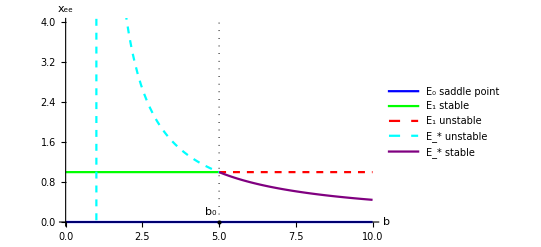

bif11T.pdf

```mathematica
ClearParameters;
λ=0.36;β=0.11;δ=0.44;bL=10;
Print["b0=",bs1//N]
fpT//N;
linb0=Line[{{ bs1,0},{ bs1,10}}];
lib0=Graphics[{Thick,Black,Dotted,linb0}];
px0=Plot[0,{b,0,bL},PlotStyle->{Blue},PlotRange->All,PlotLegends->{"E_0 saddle point"}];
px1a=Plot[{1},{b,0,bs1},PlotStyle->{Green},PlotRange->All,PlotLegends->{"E_1 stable"}];
px1b=Plot[1,{b,bs1,bL},PlotStyle->{Red,Dashed},PlotRange->All,
PlotLegends->{"E_1 unstable"}];
pxe1=Plot[{x/.fpT[[3]]},{b,0, bs1},PlotStyle->{Cyan,Dashed},PlotRange->All,
PlotLegends->{"E_* unstable"}];
pxe2=Plot[{x/.fpT[[3]]},{b,bs1, bL},PlotStyle->{Purple},PlotRange->All,
PlotLegends->{"E_* stable"}];
bif11T=Show[{px0,px1a,px1b,pxe1,pxe2,lib0},Epilog->{Text["b_0",Offset[{-8,10},{ bs1,0}]],
{PointSize[Large],Style[Point[{ bs1,0}],Purple]}},
PlotRange->{{0,10},{0,4}},AxesLabel->{"b","x_ee"}]
Export["bif11T.pdf",bif11T]
```

Periodic x,y values when b=28:

{{x→0.,y→0.,v→0.},{x→1.,y→0.,v→0.},{x→0.148148,y→0.0431317,v→2.64672}}

{-1.51022,0.000296187+0.298909 ⅈ,0.000296187-0.298909 ⅈ}

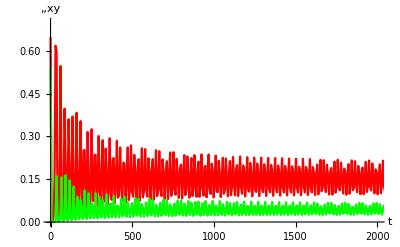

Fig5T.pdf

```mathematica
ClearParameters;
λ=0.36;β=0.11;δ=0.44;b=28;
in={x->0.5,y->0.5,v->1.5};
fpT//N
EcoEigenvalues[fpT[[3]]](*Eigenvalues corresponding to E_*  **)
solE3=EcoSim[RuleListAdd[fpT[[3]],in],20000];

Fig5T=PlotDynamics[{solE3[[1]],solE3[[2]]},PlotRange->{{0,2000},{0,0.7}}]
Export["Fig5T.pdf",Fig5T]
```

Numerical illustrations (Parametric plot) when b=28:

E*{0.148148,0.0431317,2.64672}

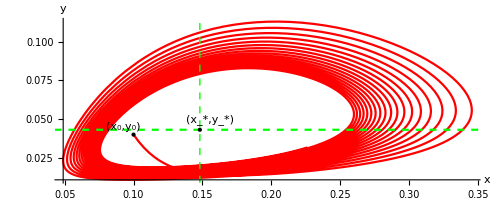

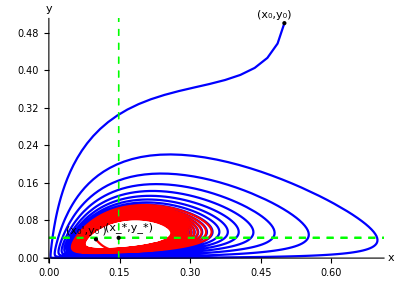

cy11.pdf

```mathematica
ClearParameters;
λ=0.36;β=0.11;δ=0.44;b=28;K=1;γ=1;
Print["E*",fp[[3]]//N]
x1=λ  x[t](1-(x[t]+y[t]))-   β x[t] v[t] ;
y1=β x[t] v[t] -  y[t];
v1=-β x[t] v[t] + b   y[t] - δ v[t];

ode={x'[t]==x1,y'[t]==y1,v'[t]==v1,x[0]==0.5,y[0]==0.5,v[0]==1.5};
sol=NDSolve[ode,{x,y,v},{t,0,400}];

x0=0.5; y0=0.5;v0=1.5;
ppb28=ParametricPlot[{  x[t],(y[t])}/.sol,{t,0,400}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py=Plot[(y/.y->fp[[3,2]]),{t,0,400},PlotStyle->{Dashed,Green}];
pb28=Show[{ppb28,py, Graphics[{Green,Dashed,
Line[{{x/.x->fp[[3,1]],0},{x/.x->fp[[3,1]],1}}]}] },
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}]],
{PointSize[Large],Style[Point[{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}];
(****************b=28; different initial values   ******************)
ClearParameters;
λ=0.36;β=0.11;δ=0.44;b=28;K=1;γ=1;

ode={x'[t]==x1,y'[t]==y1,v'[t]==v1,x[0]==0.1,y[0]==0.04,v[0]==0.01};
sol=NDSolve[ode,{x,y,v},{t,0,400}];

(*****¨Parametric plot conditions***)
x0=0.1; y0=0.04;v0=0.01;
ppb28n=ParametricPlot[{  x[t],(y[t])}/.sol,{t,0,400}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Red}];
pyn=Plot[(y/.y->fp[[3,2]]),{t,0,200},PlotStyle->{Dashed,Green}];
pb28n=Show[{ppb28n,pyn, Graphics[{Green,Dashed,
Line[{{x/.x->fp[[3,1]],0},{x/.x->fp[[3,1]],1}}]}] },
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}]],
{PointSize[Large],Style[Point[{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]
cy11=Show[{pb28,pb28n},Epilog->{Text["(x_*,y_*)",
Offset[{10,10},{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}]],
{PointSize[Large],Style[Point[{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}],Black]},
{PointSize[Large],Point[{0.1,0.04}]},Text["(x_0',y_0')",Offset[{-10,8},{0.1,0.04}]],
{PointSize[Large],Point[{0.5,0.5}]},Text["(x_0,y_0)",Offset[{-10,8},{0.5,0.5}]]}]
Export["cy11.pdf",cy11]
```

### 2)Sections 3 and 4(in paper): Four-dim viro-therapy model with Logistic growth ( when ϵ=0)

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
(*Some aliases*)
Format[μv]:=Subscript[μ,v];Format[μy]:=Subscript[μ,y];
parE={β>0,λ>0,γ>0,δ>0,μ>0, μv>0,b>1,K>0,s>0,c>0};
cKga1={ϵ->0,K->1,γ->1};
cE={ϵ->1};
R0=b β K/(β K+δ)(* Reproduction number*);
cnT17={μv->0.16, μy->0.48,K->1,γ->1,b->9,β->0.11,λ->0.36,δ->0.2,s->0.6, c->0.036}(*Numerical values of Tian17*);
```

### 2-1)Description of the model when ϵ=0 and analysis of the stability of the fixed point when z->0

```mathematica
(****** Four dim Deterministic  epidemic model with Logistic growth ****)
x1=λ  x(1-(x+y)/K)-   β x v ;
y1=β x v -μy y z- γ y;
v1=-β x v - μv  v z+ b  γ y - δ v;
z1=z(s  y - c );
ye=c/s; vM=λ(1-ye)/β;vMN=vM/.cnT17;
dyn={x1,y1,v1,z1};
dyn3={x1,y1,v1}/.z->0;(*3dim case*)
Print[" (x'
y'
v'
z')=",dyn//FullSimplify//MatrixForm, "  the reparametrized model is (x'
y'
v'
z')=",
 dyn//.cKga1//FullSimplify//MatrixForm]
Print["b0=",b0=b/.Apart[Solve[R0==1,b][[1]]//FullSimplify]]
(*****Fixed points of Tian17 using the elimination when K=1, γ=1***)

fv=(ye (b-1)-v δ); gv=(ye μy+v μv); hv=(1-ye-v β/λ);

Print["xe= ",xe=hv," ze =", ze=fv/gv]

Pv=Numerator[Together[v β xe-ye (1+μy fv/gv)]]/(-s^2 β^2 μv);
Print["P(v)=",pc=Collect[Together[Pv],v]," coefs are"]
coP=CoefficientList[pc,v]//Simplify

(***Fixed point when z->0**)
eq=Thread[dyn3=={0,0,0}];
sol=Solve[eq,{x,y,v}]//FullSimplify;
Es={x,y,v}/.sol[[3]];(*Endemic point with z=0*);
Print[" E*=",Es//FullSimplify]
Est=Es/.cKga1//FullSimplify(* E* when K=γ=1***);
Print["Check: when K=γ=1, E*=",Est]

bn=b/.Solve[Est[[2]]==ye,b]; bnn=bn/.cnT17;
bcn=b/.Solve[Est[[2]][[1]]==ye,b];
bcnn=bn/.cnT17;

Dis=Chop[Collect[Discriminant[Numerator[Pv],v],b]];
solb=Solve[Dis==0,b];
Jac=Grad[dyn/.cKga1,{x,y,v,z}]//FullSimplify;
```

(x'
y'
v'
z')=(-v x β+x (1-(x+y)/K) λ
v x β-y (γ+z μ_y)
b y γ-v (x β+δ+z μ_v)
(-c+s y) z)  the reparametrized model is (x'
y'
v'
z')=(-x (v β+(-1+x+y) λ)
v x β-y (1+z μ_y)
b y-v (x β+δ+z μ_v)
(-c+s y) z)

b0=1+δ/(K β)

xe= 1-c/s-(v β)/λ ze =(((-1+b) c)/s-v δ)/(v μ_v+(c μ_y)/s)

P(v)=v^3+(b c^2 λ μ_y)/(s^2 β^2 μ_v)+(v^2 (c s β λ μ_v-s^2 β λ μ_v+c s β^2 μ_y))/(s^2 β^2 μ_v)+(v (c s λ μ_v+c^2 β λ μ_y-c s β λ μ_y-c s δ λ μ_y))/(s^2 β^2 μ_v) coefs are

{(b c^2 λ μ_y)/(s^2 β^2 μ_v),(c λ (c β μ_y+s (μ_v-(β+δ) μ_y)))/(s^2 β^2 μ_v),(c λ μ_v-s λ μ_v+c β μ_y)/(s β μ_v),1}

E*={δ/((-1+b) β),(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)),(γ ((-1+b) K β-δ) λ)/(β ((-1+b) K β γ+δ λ))}

Check: when K=γ=1, E*={δ/((-1+b) β),(((-1+b) β-δ) δ λ)/((-1+b) β ((-1+b) β+δ λ)),(((-1+b) β-δ) λ)/(β ((-1+b) β+δ λ))}

### 2-2)Interior equilibrium

Analysis of the stability of the interior point E_*:

```mathematica
Jac3=Grad[dyn3/.cKga1,{x,y,v}]//FullSimplify;
bcrit=1+δ/(β );(*Reduce[Join[{R0>1},pars],δ]*)
Print["J(E_*) is"]
Jst=(Jac3/.x->Est[[1]]/.y->Est[[2]]/.v->Est[[3]])//FullSimplify;Jst//MatrixForm
Trs=Tr[Jst];
pc=Collect[Det[ψ IdentityMatrix[3]-Jst],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Print["a_1=",a1=coT[[3]], ", a_2=",a2=coT[[2]], ", a_3=",a3=coT[[1]]]
H2=a1*a2-a3;
Print["H2(b0)=",H2/.b->bcrit//FullSimplify]
Print["Denominator of H2 is ",Denominator[Together[H2]]/.cKga1//FullSimplify]
ϕb=Collect[Numerator[Together[H2]]/(δ λ),b]/.cKga1;
cofi=CoefficientList[ϕb,b](*Coefficients of ϕ(b)*);
Print["value of ϕ(b) at crit b is "]
ϕb/.b->bcrit/.cKga1//FullSimplify
```

J(E_*) is

((δ λ)/(β-b β) | (δ λ)/(β-b β) | -δ/(-1+b)
(((-1+b) β-δ) λ)/((-1+b) β+δ λ) | -1 | δ/(-1+b)
((β-b β+δ) λ)/((-1+b) β+δ λ) | b | (b δ)/(1-b))

a_1=(β (-1+b+b δ)+δ λ)/((-1+b) β), a_2=(δ λ ((-1+b) β (-1+β+δ+b (1-β+δ))+((-1+b)^2 β+b δ^2) λ))/((-1+b)^2 β ((-1+b) β+δ λ)), a_3=δ (1+δ/(β-b β)) λ

H2(b0)=(1+β+δ) λ (1+β+δ+λ)

Denominator of H2 is (-1+b)^3 β^2 ((-1+b) β+δ λ)

value of ϕ(b) at crit b is

(δ^3 (1+β+δ) (1+λ) (1+β+δ+λ))/β

Numerical values:

```mathematica
cn=cnT17;
cb=NSolve[(ϕb//.Drop[cnT17,{5}])==0,b,WorkingPrecision->10]
bM=Max[Table[Re[b/.cb[[i]]],{i,Length[cb]}]];
Print["bH=",bH=N[bM,30]]
PR=Solve[Pv==0,v];
 vn=v/.PR[[2]];vi=v/.PR[[3]]; vp=v/.PR[[1]];
Chop[{vn,vi,vp}/.cnT17];
PR=Solve[Pv==0,v];
 vn=v/.PR[[2]]; vp=v/.PR[[1]];vi=v/.PR[[3]];
Print["b0=",b0/.cn//N, " , b1=", bnn[[1]],   ", b2=", bnn[[2]], "  ,bH=",bH]
PRN=Chop[PR//.cn//N](*values of the roots v*);
Print["E*",Es=Es/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]

Jiv=Jac//.{x->xe,y->ye,z->ze};
JEi=Jiv/.v->vi//.cn//N//FullSimplify;
JEp=Jiv/.v->vp//.cn//N//FullSimplify;
JEif=Jac/.x->1/.y->0/.z->0/.v->0//.cn//N//FullSimplify;
Print["Eigv of E*:",Append[Eigenvalues[Jst]//.cn//N,Es[[2]]-ye/.cnT17]," Eigv of E+:",
Re[Eigenvalues[JEp]//N], " Eigv of Ei:",Re[Eigenvalues[JEi]//N],  
"   , Eigv of Eif:",Eigenvalues[JEif]//N]
```

{{b→0.299052},{b→0.835329-0.231156 ⅈ},{b→0.835329+0.231156 ⅈ},{b→19.0121}}

bH=19.0121

b0=2.81818 , b1=3.58676, b2=8.66779  ,bH=19.0121

E*{0.227273,0.0584416,2.33766}

E+={0.249944,0.06,2.25837,0.072607}

Ei={0.483284,0.06,1.49471,0.675711}

Eigv of E*:{-1.25056,-0.0281268-0.20904 ⅈ,-0.0281268+0.20904 ⅈ,-0.00155844} Eigv of E+:{-1.29833,-0.0332218,-0.0332218,0.000834552} Eigv of Ei:{-1.69849,-0.076539,-0.076539,-0.00803072}   , Eigv of Eif:{-1.7081,0.398103,-0.36,-0.036}

### 3)Sections 3.1---3.3(in paper):Figures used in the manuscript (*Run the previous cell*) Numerical illustrations when ϵ=0 (Bifurcations diagrams, parametric plots, and 3D plot)

Bifurcation diagram when b varies:

{b_(2*),b_(1*)}={10.2462,-0.00697038}, and b_0=2.81818  , b_H=19.012107471368075382 ,b1=3.58676, b2=8.66779

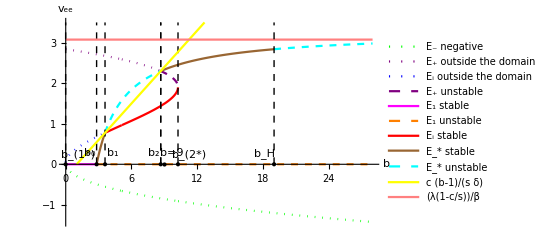

BiifT17.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=9;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["{b_(2*),b_(1*)}=",{b/.solb[[1]],b/.solb[[2]]} ,", and b_0=",b0, "  , b_H=",bH,   
 " ,b1=", bnn[[1]],   ", b2=", bnn[[2]]]
Clear["b"];
vs=(((-1+b) β-δ) λ)/(β ((-1+b) β+δ λ))(*v of E* *  ****);
bL=28; max=3.5;
bc2=b/.solb[[1]];
bc1=b/.solb[[2]];
lin1=Line[{{ bc1,0},{ bc1,max}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,max}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
lin3=Line[{{ b0,0},{ b0,max}}];
li3=Graphics[{Thick,Black,Dashed,lin3}];
linH=Line[{{ bH,0},{ bH,max}}];
liH=Graphics[{Thick,Black,Dashed,linH}];
linb1=Line[{{ bnn[[1]],0},{ bnn[[1]],max}}];
lib1=Graphics[{Thick,Black,Dashed,linb1}];
linb2=Line[{{ bnn[[2]],0},{ bnn[[2]],max}}];
lib2=Graphics[{Thick,Black,Dashed,linb2}];
linb9=Line[{{ 9,0},{9,max}}];
lib9=Graphics[{Thick,Black,Dashed,linb2}];
pn=Plot[{vn},{b,0,bL},PlotStyle->{Green,Dotted},PlotRange->All,PlotLegends->{"E_- negative"}];
p0=Plot[0,{b,0,bL},PlotStyle->{Brown,Thick},PlotRange->All,PlotLegends->{"E_0 saddle point"}];
ppa=Plot[{vp},{b,0, bnn[[2]]},PlotStyle->{Purple,Dotted},PlotRange->All,
PlotLegends->{"E_+ outside the domain"}];
ppb=Plot[{vp},{b,bnn[[2]], bL},PlotStyle->{Purple,Thick,Dashed},
PlotRange->All,PlotLegends->{"E_+ unstable"}];
pi1=Plot[{vi},{b,0,bnn[[1]]},PlotStyle->{Blue,Dotted},
PlotRange->All,PlotLegends->{"E_i outside the domain"}];
pi2=Plot[{vi},{b,bnn[[1]],bL},PlotStyle->{Red,Thick},
PlotRange->All,PlotLegends->{"E_i stable"}];
pi3=Plot[{vi},{b,bnn[[2]],bL},PlotStyle->{Blue,Thick,Dashed},
PlotRange->All(*,PlotLegends->{"E_i unstable"}*)];
ps1=Plot[{vs},{b,b0,bnn[[1]]},PlotStyle->{Brown,Thick},
PlotRange->{{0,bL},{0,max}},PlotLegends->{"E_* stable"}];
ps2=Plot[{vs},{b,bnn[[1]],bnn[[2]]},PlotStyle->{Cyan,Thick,Dashed},
PlotRange->{{0,bL},{0,max}},PlotLegends->{"E_* unstable"}];
ps3=Plot[{vs},{b,bnn[[2]],bH},PlotStyle->{Brown,Thick},
PlotRange->{{0,bL},{0,max}}(*,PlotLegends->{"E_* stable"}*)];
ps4=Plot[{vs},{b,bH,bL},PlotStyle->{Cyan,Thick,Dashed},
PlotRange->{{0,bL},{0,max}}(*,PlotLegends->{"E_* unstable"}*)];
pdf1=Plot[{0},{b,0,b0},PlotStyle->{Magenta, Thick},
PlotRange->{{0,200},{0,max}},PlotLegends->{"E_1 stable"}];
pdf2=Plot[{0},{b,b0,bL},PlotStyle->{Orange, Thick,Dashed},
PlotRange->{{0,200},{0,max}},PlotLegends->{"E_1 unstable"}];
pvmax=Plot[{c (b-1)/(s δ),(λ(1-c/s))/β},{b,0,bL},PlotStyle->{Yellow, Pink},
PlotRange->{{0,200},{0,max}},
PlotLegends->{"c (b-1)/(s δ)","(λ(1-c/s))/β"}];

bifT=Show[{pn,ppa,pi1,ppb,pdf1,pdf2,pi2,ps1,ps2,ps3,ps4,li1,li2,li3,
lib2,lib1,lib9,pvmax,liH},
Epilog->{Text["b_(1*)",Offset[{12,10},{ bc1,0}]],{PointSize[Large],
Style[Point[{ bc1,0}],Purple]},
Text["b_(2*)",Offset[{11,10},{ bc2,0}]],{PointSize[Large],Style[Point[{ bc2,0}],Yellow]},
Text["b_0",Offset[{-7,11},{ b0,0}]],{PointSize[Large],Style[Point[{ b0,0}],Black]},
Text["b_H",Offset[{-10,11},{ bH,0}]],{PointSize[Large],Style[Point[{ bH,0}],Green]},
Text["b_1",Offset[{8,11},{ bnn[[1]],0}]],{PointSize[Large],Style[Point[{ bnn[[1]],0}],Pink]},
Text["b_2",Offset[{-7,11},{ bnn[[2]],0}]],{PointSize[Large],Style[Point[{ bnn[[2]],0}],Red]},
Text["b=9",Offset[{7,11},{9,0}]],{PointSize[Large],Style[Point[{ 9,0}],Brown]}},
PlotRange->All,AxesLabel->{"b","v_ee"}]
Export["BiifT17.pdf",bifT]
```

Parametric plots at the intervals of stability:

When b0<b=3<b1:

E*{0.909091,0.0224159,0.224159}

E+={0.113348,0.06,2.70541,-0.912093}

Ei={0.726116,0.06,0.699984,-0.142026}

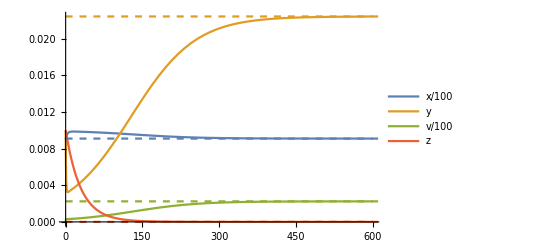

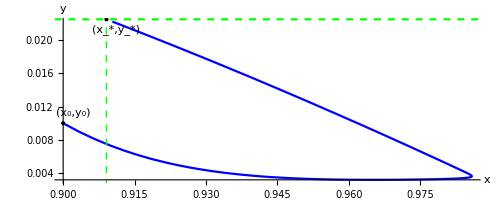

pb3.pdf

Dyn01.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=3;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;

Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]
x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );
ode1={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.9,y[0]==0.01,v[0]==0.01,
z[0]==0.01};
sol01=NDSolve[ode1,{x,y,v,z},{t,0,500}];
pdy1=Plot[{x[t]/100/. sol01,y[t]/. sol01,v[t]/100/. sol01,z[t]/. sol01},
{t,0,600},PlotLegends->{"x/100","y","v/100","z"}];
pEs1=Plot[{x/100/.x->Es[[1]],y/.y->Es[[2]],v/100/.v->Es[[3]],z/.z->0},{t,0,1000},
PlotStyle->{Dashed}];
Dyn01=Show[pdy1,pEs1]

(*****¨Parametric plot conditions***)
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
ppb3=ParametricPlot[{  x[t],(y[t])}/.sol01,{t,0,400}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py3=Plot[y/.y->Es[[2]],{t,0,400},PlotStyle->{Dashed,Green}];
pb3=Show[{ppb3,py3, Graphics[{Green,Dashed,Line[{{x/.x->Es[[1]],0},{x/.x->Es[[1]],1}}]}] },
Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,-10},{x/.x->Es[[1]],y/.y->Es[[2]]}]],
{PointSize[Large],Style[Point[{x/.x->Es[[1]],y/.y->Es[[2]]}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{10,10},{x0,y0}]]}]
Export["pb3.pdf",pb3]
Export["Dyn01.pdf",Dyn01]
```

When b1<b=6<b2:

E*{0.363636,0.0736627,1.84157}

E+={0.166196,0.06,2.53245,-0.475792}

Ei={0.612063,0.06,1.07325,0.425644}

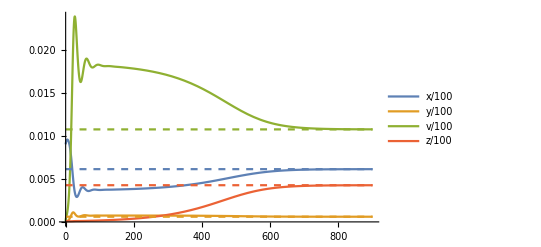

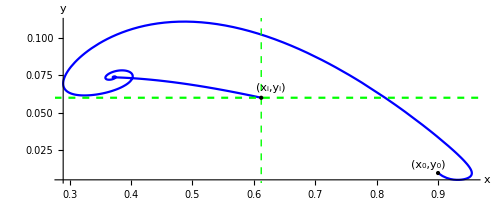

Dyn12.pdf

pb6.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=6;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]

x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );
ode2={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.9,y[0]==0.01,v[0]==0.01,
z[0]==0.01};
sol12=NDSolve[ode2,{x,y,v,z},{t,0,1000}];
pdy1=Plot[{x[t]/100/. sol12,y[t]/100/. sol12,v[t]/100/. sol12,z[t]/100/. sol12},
{t,0,900},PlotLegends->{"x/100","y/100","v/100","z/100"}];
pEs1=Plot[{x/100/.x->Ei[[1]],y/100/.y->Ei[[2]],v/100/.v->Ei[[3]],z/100/.z->Ei[[4]]},{t,0,900},
PlotStyle->{Dashed}];
Dyn12=Show[pdy1,pEs1]
(*****¨Parametric plot conditions***)
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
startP=Epilog->{{PointSize[Large],Point[{0.9,0.01}]},Text["(x_0,y_0)",
Offset[{0,10},{0.9,0.01}]]};
bnd =Thread[{x[0],y[0],v[0],z[0]}=={x0,y0,v0,z0}](*Starting point of the Paramateric Plot**);
ppb6=ParametricPlot[{  x[t],(y[t])}/.sol12,{t,0,900}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py6=Plot[(y/.y->Ei[[2]]),{t,0,1000},PlotRange->{{0,0.612},{0,0.08}},PlotStyle->{Dashed,Green}];
pb6=Show[{ppb6,py6, Graphics[{Green,Dashed,Line[{{x/.x->Ei[[1]],0},{x/.x->Ei[[1]],1}}]}] },
Epilog->{{Text["(x_i,y_i)",Offset[{10,10},{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}]],
{PointSize[Large],Style[Point[{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}],Black]}},
{PointSize[Large],Point[{0.9,0.01}]},Text["(x_0,y_0)",Offset[{-10,8},{0.9,0.01}]]}]
Export["Dyn12.pdf",Dyn12]
Export["pb6.pdf",pb6]
```

When b2<b=9<b2*:

E*{0.227273,0.0584416,2.33766}

E+={0.249944,0.06,2.25837,0.072607}

Ei={0.483284,0.06,1.49471,0.675711}

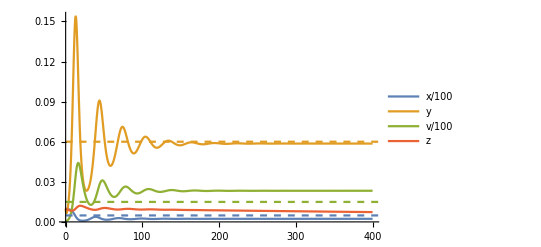

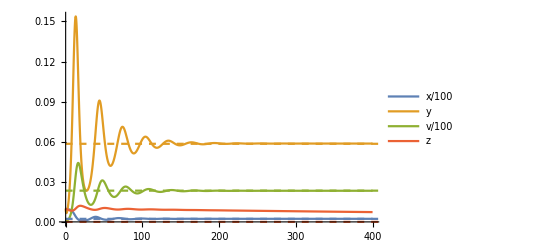

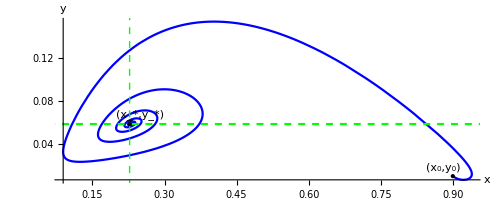

pb9.pdf

Dyni22.pdf

Dyns22.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=9;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]

x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );
ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.9,y[0]==0.01,v[0]==0.01,
z[0]==0.01};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,400}];
pdy2=Plot[{x[t]/100/. sol22,y[t]/. sol22,v[t]/100/. sol22,z[t]/. sol22},{t,0,400},
PlotLegends->{"x/100","y","v/100","z"}];
pEs2=Plot[{x/100/.x->Es[[1]],y/.y->Es[[2]],v/100/.v->Es[[3]],z/.z->0},{t,0,1000},
PlotStyle->{Dashed}];
pEi2=Plot[{x/100/.x->Ei[[1]],y/.y->Ei[[2]],v/100/.v->Ei[[3]],z/.z->Ei[[4]]},{t,0,1000},
PlotStyle->{Dashed}];
Dyni22=Show[pdy2,pEi2]
Dyns22=Show[pdy2,pEs2]

(*****¨Parametric plot conditions***)
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
ppb9=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,200}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py9=Plot[(y/.y->Es[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb9=Show[{ppb9,py9, Graphics[{Green,Dashed,Line[{{x/.x->Es[[1]],0},{x/.x->Es[[1]],1}}]}] },
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),(y/.y->Es[[2]])}]],{PointSize[Large],
Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Black]}},{PointSize[Large],Point[{0.9,0.01}]},
Text["(x_0,y_0)",Offset[{-10,8},{0.9,0.01}]]}]
Export["pb9.pdf",pb9]
Export["Dyni22.pdf",Dyni22]
Export["Dyns22.pdf",Dyns22]
```

When b2<b=9<b2*  and different initial values :

E*{0.227273,0.0584416,2.33766}

E+={0.249944,0.06,2.25837,0.072607}

Ei={0.483284,0.06,1.49471,0.675711}

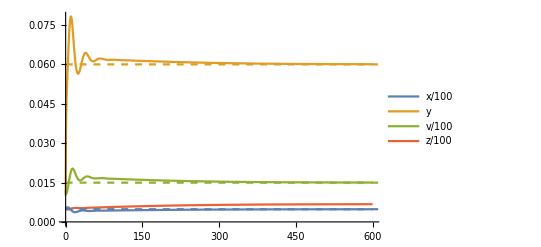

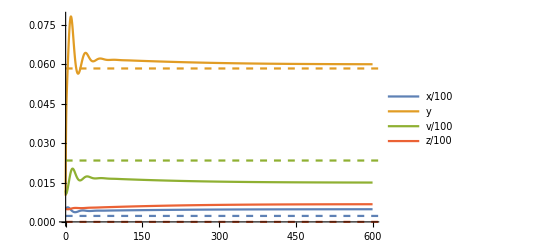

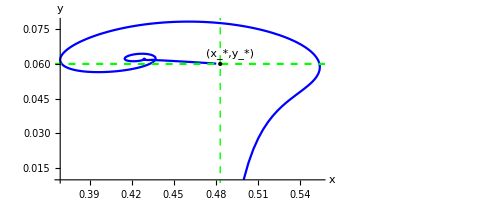

pb9i.pdf

Dyni22b.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=9;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]

x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );
ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.5,y[0]==0.01,v[0]==1.2,
z[0]==0.5};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,1000}];
pdy2=Plot[{x[t]/100/. sol22,y[t]/. sol22,v[t]/100/. sol22,z[t]/100/. sol22},{t,0,600},
PlotLegends->{"x/100","y","v/100","z/100"}];
pEs2=Plot[{x/100/.x->Es[[1]],y/.y->Es[[2]],v/100/.v->Es[[3]],z/.z->0},{t,0,1000},
PlotStyle->{Dashed}];
pEi2=Plot[{x/100/.x->Ei[[1]],y/.y->Ei[[2]],v/100/.v->Ei[[3]],z/.z->Ei[[4]]},{t,0,1000},
PlotStyle->{Dashed}];
Dyni22b=Show[pdy2,pEi2]
Dyns22=Show[pdy2,pEs2]

(*****¨Parametric plot conditions***)
x0=0.5; y0=0.01;v0=1.2;z0=0.5;
ppb9=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,500}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py9=Plot[(y/.y->Ei[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb9i=Show[{ppb9,py9, Graphics[{Green,Dashed,Line[{{x/.x->Ei[[1]],0},{x/.x->Ei[[1]],1}}]}] },
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}]],{PointSize[Large],
Style[Point[{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}],Black]}},{PointSize[Large],Point[{0.9,0.01}]},
Text["(x_0,y_0)",Offset[{-10,8},{0.9,0.01}]]}]
Export["pb9i.pdf",pb9i]
Export["Dyni22b.pdf",Dyni22b]
```

When b2<b=10<b2*:

E*{0.20202,0.0541003,2.43451}

E+={0.30876,0.06,2.06588,0.352938}

Ei={0.411479,0.06,1.72971,0.635108}

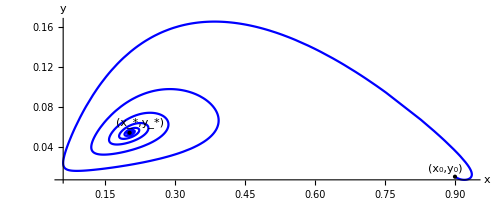

pb10.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=10;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]

x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );

ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.9,y[0]==0.01,v[0]==0.01,
z[0]==0.01};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,400}];


(*****¨Parametric plot conditions***)
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
ppb10=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,200}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py10=Plot[(y/.y->Es[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb10=Show[{ppb10},Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Black]}},
{PointSize[Large],Point[{0.9,0.01}]},Text["(x_0,y_0)",Offset[{-10,8},{0.9,0.01}]]}]

Export["pb10.pdf",pb10]
```

E*{0.20202,0.0541003,2.43451}

E+={0.30876,0.06,2.06588,0.352938}

Ei={0.411479,0.06,1.72971,0.635108}

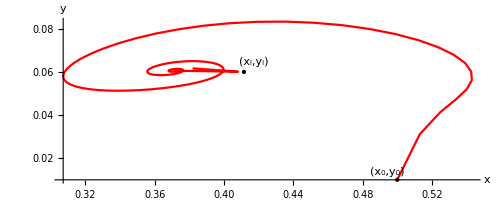

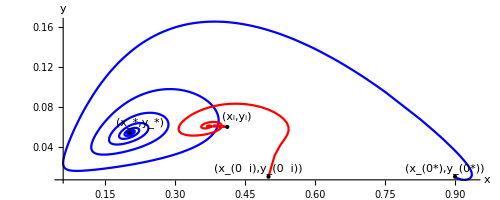

pp10si.pdf

pb10i.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=10;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]

x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );
ode3={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.5,y[0]==0.01,v[0]==1.2,
z[0]==0.5};
sol22=NDSolve[ode3,{x,y,v,z},{t,0,1000}];
x0=0.5; y0=0.01;v0=1.2;z0=0.5;
ppb10i=ParametricPlot[{  x[t],(y[t])}/.sol22,{t,0,1900}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Red}];
py10i=Plot[(y/.y->Ei[[2]]),{t,0,800},PlotStyle->{Dashed,Green}];
pb10i=Show[{ppb10i },Epilog->{{Text["(x_i,y_i)",Offset[{10,10},{(x/.x->Ei[[1]]),
(y/.y->Ei[[2]])}]],
{PointSize[Large],Style[Point[{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]
pp10si=Show[{pb10,pb10i},Epilog->{{Text["(x_i,y_i)",Offset[{10,10},{(x/.x->Ei[[1]]),
(y/.y->Ei[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Ei[[1]]),(y/.y->Ei[[2]])}],Black]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_(0  i),y_(0  i))",Offset[{-10,8},{x0,y0}]],
{Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),(y/.y->Es[[2]])}]],{PointSize[Large],
Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Black]}},{PointSize[Large],Point[{0.9,0.01}]},
Text["(x_(0*),y_(0*))",Offset[{-10,8},{0.9,0.01}]]}]
Export["pp10si.pdf",pp10si]
Export["pb10i.pdf",pb10i]
```

When b2*<b=15<bH:

E*{0.12987,0.0388644,2.72051}

E+={0.332366+0.217051 ⅈ,0.06,1.98862-0.710347 ⅈ,1.03002+0.746836 ⅈ}

Ei={0.332366-0.217051 ⅈ,0.06,1.98862+0.710347 ⅈ,1.03002-0.746836 ⅈ}

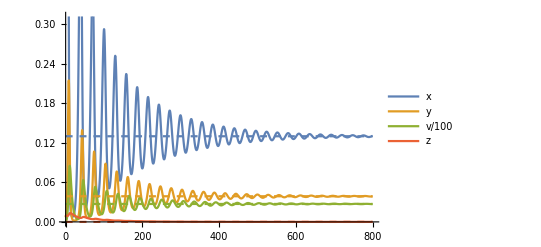

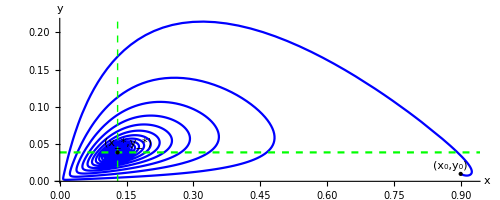

pb15.pdf

Dyn2H.pdf

```mathematica
ClearParameters;
μv=0.16; μy=0.48;K=1;b=15;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]

x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );
ode4={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.9,y[0]==0.01,v[0]==0.01,
z[0]==0.01};
sol2H=NDSolve[ode4,{x,y,v,z},{t,0,800}];
pdy2H=Plot[{x[t]/. sol2H,y[t]/. sol2H,v[t]/100/. sol2H,z[t]/. sol2H},{t,0,800},
PlotLegends->{"x","y","v/100","z"}];
pEs2H=Plot[{x/.x->Es[[1]],y/.y->Es[[2]],v/100/.v->Es[[3]],z/.z->0},{t,0,800},
PlotStyle->{Dashed}];
Dyn2H=Show[pdy2H,pEs2H,PlotRange->All]

(*****¨Parametric plot conditions***)
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
ppb15=ParametricPlot[{  x[t],(y[t])}/.sol2H,{t,0,500}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
py15=Plot[(y/.y->Es[[2]]),{t,0,400},PlotStyle->{Dashed,Green}];
pb15=Show[{ppb15,py15, Graphics[{Green,Dashed,Line[{{x/.x->Es[[1]],0},
{x/.x->Es[[1]],1}}]}] },Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Black]}}
,{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]
Export["pb15.pdf",pb15]
Export["Dyn2H.pdf",Dyn2H]
```

When bH<b=23<b∞:

E*{0.0826446,0.0265046,2.91551}

E+={0.297813+0.339863 ⅈ,0.06,2.1017-1.11228 ⅈ,1.75115+1.463 ⅈ}

Ei={0.297813-0.339863 ⅈ,0.06,2.1017+1.11228 ⅈ,1.75115-1.463 ⅈ}

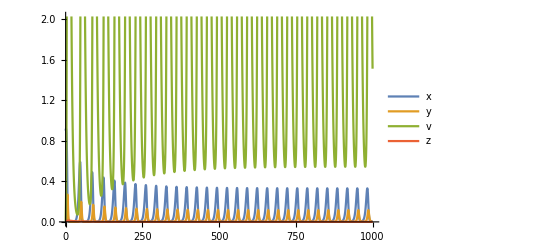

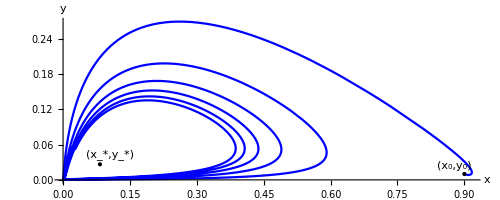

pb23.pdf

DynHI.pdf

```mathematica
ClearParameters; 
μv=0.16; μy=0.48;K=1;b=23;γ=1;λ=0.36;β=0.11;δ=0.2;s=0.6; c=0.036;ϵ=0;
Print["E*",Es=Est/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]
x1=λ  x[t](1-(x[t]+y[t])/K)-   β x[t] v[t] ;
y1=β x[t] v[t] -μy y[t] z[t]- γ y[t];
v1=-β x[t] v[t] - μv  v[t] z[t]+ b  γ y[t] - δ v[t];
z1=z[t](s  y[t] - c );
ode5={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.9,y[0]==0.01,v[0]==0.01,
z[0]==0.01};
solHI=NDSolve[ode5,{x,y,v,z},{t,0,10000}];
pdyHI=Plot[{x[t]/. solHI,y[t]/. solHI,v[t]/. solHI,z[t]/. solHI},{t,0,1000},
PlotLegends->{"x","y","v","z"}];
DynHI=Show[pdyHI,PlotRange->All]

(*****¨Parametric plot conditions***)
x0=0.9; y0=0.01;v0=0.01;z0=0.01;
ppb23=ParametricPlot[{  x[t],(y[t])}/.solHI,{t,0,200}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Blue}];
NDSolve[{y'[t]==y[t] (x[t]-1),x'[t]==x[t] (2-y[t]),x[0]==1,y[0]==2.7},{x,y},{t,0,10}];
py23=Plot[(y/.y->Es[[2]]),{t,0,400},PlotStyle->{Dashed,Green}];
pb23=Show[{ppb23},Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Green]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",Offset[{-10,8},{x0,y0}]]}]
Export["pb23.pdf",pb23]
Export["DynHI.pdf",DynHI]
```

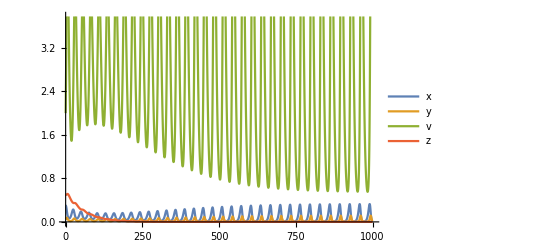

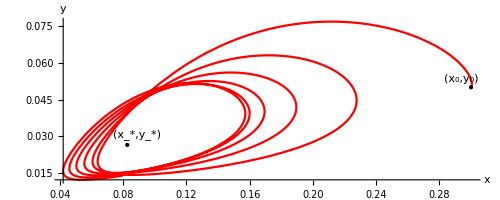

pb23b.pdf

DynHIb.pdf

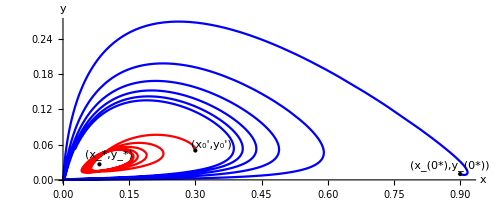

pp23s.pdf

```mathematica
ode5={x'[t]==x1,y'[t]==y1,v'[t]==v1,z'[t]==z1,x[0]==0.3,y[0]==0.05,v[0]==2,
z[0]==0.5};
solHI=NDSolve[ode5,{x,y,v,z},{t,0,10000}];
pdyHI=Plot[{x[t]/. solHI,y[t]/. solHI,v[t]/. solHI,z[t]/. solHI},{t,0,1000},
PlotLegends->{"x","y","v","z"}];
DynHIc=Show[pdyHI,PlotRange->All]
(*New initial conditions**)
x0=0.3; y0=0.05;v0=2;z0=0.5;
ppb23c=ParametricPlot[{  x[t],(y[t])}/.solHI,{t,0,150}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Red}];
pb23c=Show[{ppb23c },Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,10},
{(x/.x->Es[[1]]),(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}],Green]}},{PointSize[Large],Point[{x0,y0}]},Text["(x_0,y_0)",
Offset[{-10,8},{x0,y0}]]}]
Export["pb23b.pdf",pb23c]
Export["DynHIb.pdf",DynHIc]
pp23cs=Show[{pb23,pb23c},Epilog->{{Thick,Text["(x_*,y_*)",Offset[{10,10},{(x/.x->Es[[1]]),
(y/.y->Es[[2]])}]],{PointSize[Large],Style[Point[{(x/.x->Es[[1]]),(y/.y->Es[[2]])}],Green]}},
{PointSize[Large],Point[{x0,y0}]},Text["(x_0',y_0')",Offset[{16,6},{x0,y0}]],
{PointSize[Large],Point[{0.9,0.01}]},Text["(x_(0*),y_(0*))",Offset[{-10,8},{0.9,0.01}]]}]
Export["pp23s.pdf",pp23cs]
```

3D- Plot of the dynamic:

```mathematica
cn=cnT17;
Print["E*",Es=Es/.cn//N]
Print["E+=",Ep=Chop[{xe,ye,v,ze}/.v->vp/.cn//N]]
Print["Ei=",Ei=Chop[{xe,ye,v,ze}/.v->vi/.cn//N]]
epi={Text["E_*",Offset[{-10,10},{Es[[1]],Es[[2]]}]]//.cn,
{PointSize[Large],Style[Point[{Es[[1]],Es[[2]]}],Blue]//.cn},Text["E_i",Offset[{0,10},
{Ei[[1]],Ei[[2]]}]],{PointSize[Large],Style[Point[{Ei[[1]],Ei[[2]]}],Purple]},
Text["E_+",Offset[{0,10},{Ep[[1]],Ep[[2]]}]],{PointSize[Large],
Style[Point[{Ep[[1]],Ep[[2]]}],Orange]}};
sp3=StreamPlot3D[dyn3//.cnT17,{x,0,1},{y,0,1},{v,0,3},AxesLabel->{"x","y","v"},
 StreamColorFunction->Hue,PlotRange->All,StreamMarkers->"Arrow3D",StreamScale->Full];
sp3D=Show[{sp3},Graphics3D[Text[Style["E_*",Black,Thick],Es//.cn],
{PointSize[0.06],Style[Point[Es],Black]}],Graphics3D[Text[Style["E_i",Black,Thick],
Drop[Ei,{4}]//.cn],{PointSize[0.06],Style[Point[Drop[Ei,{4}]],Black]}]]
Export["sp3D.pdf",sp3D]
```

E*{0.227273,0.0584416,2.33766}

E+={0.249944,0.06,2.25837,0.072607}

Ei={0.483284,0.06,1.49471,0.675711}

-Graphics3D-

sp3D.pdf

## 4)Section 3.4(in paper): 4-Dim.Viro-therapy model when ϵ=1

### 4-1)Definition of the model and fixed points when ϵ=1

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
Clear["K"];
Format[μv]:=Subscript[μ,v];Format[μy]:=Subscript[μ,y];Format[La]:=Λ;(*La >0*)
pars={β,λ,γ,δ,μy, μv,b,K,s,c};
cpos={β>0,λ>0,γ>0,δ>0,μy>0, μv>0,b>1,K>0,s>0,c>0};
La=0; bL=100;cnb={b->50};
cEri={μy->1/48,K->2139.258, β->.0002,λ->.2062,γ->1/18,δ->.025, μv->2*10^(-8),c->10^(-3),s->.027};
(****** Four dim Deterministic  epidemic model with Logistic growth ****)
x1=La+λ  x(1-(x+y)/K)-   β x v ;
y1=β x v -μy y z- γ y;
v1=-β x v - μv  v z+ b  γ y - δ v;
z1=z(s  y - c z);
x1s=λ  (1-(x+y)/K)-   β  v ;
z1s=s y - c z;
dyns={x1s,y1,v1,z1s};
dyn={x1,y1,v1,z1};
dyn3={x1,y1,v1}/.z->0;
Print[" (x'
y'
v'
z')=",dyn//FullSimplify//MatrixForm]

(*Jacobian*)
Jac=Grad[(dyn),{x,y,v,z}]//FullSimplify;
Print["J(x,y,v,z)=",Jac//MatrixForm]
Print["J(E0)=",Jac//.Thread[{x,y,v,z}->{0,0,0,0}]//MatrixForm]
Jac3=Grad[(dyn3),{x,y,v}]//FullSimplify;
det=Det[Jac]//FullSimplify; tr=Tr[Jac]//FullSimplify;
R0=b β K/(β K+δ);bcrit=1+δ/(β K);(*Reduce[Join[{R0>1},pars],δ]*)
(****Endemic points in 3dims **)
eqE=Thread[dyn3=={0,0,0}];
Print["Three Fixed points in 3-dim case:",solE=Solve[eqE,{x,y,v}]//FullSimplify]

el=Eliminate[Thread[dyns=={0,0,0,0}],{x,v,z}];
Qybyelim=Factor[el[[1,1]]-el[[1,2]]]/y//FullSimplify;
Print["Coefficients of  Qy by elim polynomial are:"]
cof=CoefficientList[Qybyelim,y]//FullSimplify
so=y/.Solve[Qybyelim==0,y];(*Third order roots*)

(*****Fixed points of 4-dim model using P(y)***)
fy=(c γ(b-1)-y μy s);
gy=( μv s y+c δ); hy=(γ +y s μy/c);
xe=hy gy/(β fy); ve=y fy/gy; ze= s y /c;
ys=y/.solE[[3]](* y of E*     ****);

Py=λ(1-y/K)-β y fy/gy-λ hy gy/(β K fy); yb=c γ (b-1)/(μy s);
Qy=λ fy gy(1-  y /K)- λ hy gy^2/(β K)-y β fy^2//FullSimplify;
Qycol=Collect[Qy,y];
Qycoef=CoefficientList[Qycol,y];
(*Print["Check Eric Qy -elim Qy=",Qybyelim+c K β Qy//FullSimplify]*)
Dis=Collect[Discriminant[Qy,y],b];
Discoef=CoefficientList[Dis,b];Length[Discoef];
DisE=Dis//.cEri//N;
```

(x'
y'
v'
z')=(-v x β+x (1-(x+y)/K) λ
v x β-y (γ+z μ_y)
b y γ-v (x β+δ+z μ_v)
z (s y-c z))

J(x,y,v,z)=(-v β+λ-((2 x+y) λ)/K | -(x λ)/K | -x β | 0
v β | -γ-z μ_y | x β | -y μ_y
-v β | b γ | -x β-δ-z μ_v | -v μ_v
0 | s z | 0 | s y-2 c z)

J(E0)=(λ | 0 | 0 | 0
0 | -γ | 0 | 0
0 | b γ | -δ | 0
0 | 0 | 0 | 0)

Three Fixed points in 3-dim case:{{x→0,y→0,v→0},{x→K,y→0,v→0},{x→δ/((-1+b) β),y→(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)),v→(γ ((-1+b) K β-δ) λ)/(β ((-1+b) K β γ+δ λ))}}

Coefficients of  Qy by elim polynomial are:

{c^3 γ δ (K (β-b β)+δ) λ,c^2 ((-1+b) c β γ ((-1+b) K β γ+δ λ)+s λ (γ (K (β-b β)+2 δ) μ_v+δ (K β+δ) μ_y)),c s (s λ μ_v (γ μ_v+K β μ_y+2 δ μ_y)+c β (-δ λ μ_y+(-1+b) γ (λ μ_v-2 K β μ_y))),s^2 μ_y (s λ μ_v^2+c β (-λ μ_v+K β μ_y))}

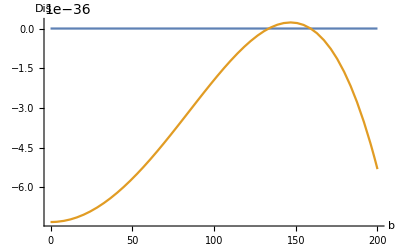

Roots of Dis[b]=0 are: {{b→-468749.},{b→-468749.},{b→-159.797},{b→-132.005},{b→133.421},{b→159.122}}

critical b from R0=1 is:1.02299

J(EK)=(-λ | -λ | -K β | 0
0 | -γ | K β | 0
0 | b γ | -K β-δ | 0
0 | 0 | 0 | 0)

Eig.val of J(EK) are:{0,1/2 (-K β-γ-δ-√(-4 γ (K (β-b β)+δ)+(K β+γ+δ)^2)),1/2 (-K β-γ-δ+√(-4 γ (K (β-b β)+δ)+(K β+γ+δ)^2)),-λ}

```mathematica
Plot[{0,DisE},{b,0,2 bL},AxesLabel->{"b","Dis"}]
Print["Roots of Dis[b]=0 are: ",solbE=Solve[DisE==0,b]]
QR=Solve[Qy==0,y];
Print["critical b from R0=1 is:", bcrit//.cEri//N]
ym= y/.QR[[1]];
yp=  y/.QR[[2]];yi=  y/.QR[[3]];

{Chop[yp],Chop[ym]}//.cEri//Simplify;

jacEK=Jac/.x->K/.y->0/.v->0/.z->0;
Print["J(EK)=", jacEK//MatrixForm]
Print["Eig.val of J(EK) are:", Eigenvalues[jacEK]//FullSimplify]
```

### 4-2)Stability of the interior points using Routh Hurwitz:

```mathematica
jacE=Jac/.x->xe/.v->ve/.z->ze/.y->y;
jacE //FullSimplify//MatrixForm
Print["Det[Jac]=",Det[jacE]//FullSimplify, " , Trace[Jac]=",
Tr[jacE]//FullSimplify]
(*Reduce[Join[{Det[Jac]>0&&x>0&&y>0&&z>0&&v>0},cpos],β](*take so long time**)*)
(*Reduce[Join[{Tr[jacE]<0&&x>0&&y>0&&z>0&&v>0},cpos],β];
poly=Collect[Together[Det[ψ IdentityMatrix[4]-jacE]],ψ];
coe=CoefficientList[poly,ψ];*) 
(*Print["Coefficients of the Characteristic polynomial are:",coe]*)
```

(λ+(y β (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v)-(λ (y+(2 (c δ+s y μ_v) (γ+(s y μ_y)/c))/(β ((-1+b) c γ-s y μ_y))))/K | -(λ (c δ+s y μ_v) (γ+(s y μ_y)/c))/(K β ((-1+b) c γ-s y μ_y)) | -((c δ+s y μ_v) (γ+(s y μ_y)/c))/((-1+b) c γ-s y μ_y) | 0
(y β ((-1+b) c γ-s y μ_y))/(c δ+s y μ_v) | -(c γ+s y μ_y)/c | ((c δ+s y μ_v) (γ+(s y μ_y)/c))/((-1+b) c γ-s y μ_y) | -y μ_y
(y β (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v) | b γ | (b γ (c δ+s y μ_v))/(c (γ-b γ)+s y μ_y) | (y μ_v (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v)
0 | (s^2 y)/c | 0 | -s y)

Det[Jac]=-1/(c^3 K β ((-1+b) c γ-s y μ_y)^2)s y^2 (-(-1+b)^2 c^5 β γ^3 ((-1+b) K β γ+δ λ)+2 s^5 y^4 λ μ_v^2 μ_y^3+c s^4 y^3 μ_y^2 (2 (3-2 b) γ λ μ_v^2+2 (-y β+δ) λ μ_v μ_y+K β μ_y (λ μ_v+2 y β μ_y))-c^2 s^3 y^2 μ_y (6 (-1+b) γ^2 λ μ_v^2+y β δ λ μ_y^2+γ μ_y ((3 (-1+b) K β+(6-5 b) y β+6 (-1+b) δ) λ μ_v+(-7+6 b) K y β^2 μ_y))-c^3 s^2 y γ (2 (-1+b) γ^2 λ μ_v^2+δ (3 y β+b (K β-3 y β+2 δ)) λ μ_y^2+γ μ_y ((3 (-2+b) (-1+b) y β-6 δ+8 b δ) λ μ_v-(-1+b) (-3+2 b) K β (λ μ_v+3 y β μ_y)))+c^4 s γ^2 (-2 (-1+b) γ ((-1+b) y β+δ) λ μ_v-δ ((-1+b) (-3+2 b) y β+2 b δ) λ μ_y+(-1+b) K β (b δ λ μ_y+(-1+b) γ (λ μ_v+(5-2 b) y β μ_y)))) , Trace[Jac]=-s y-γ-δ+λ-(s y μ_v)/c-(s y μ_y)/c+(y β (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v)-((c δ+s y μ_v) (γ+(s y μ_y)/c))/((-1+b) c γ-s y μ_y)-(λ (y+(2 (c δ+s y μ_v) (γ+(s y μ_y)/c))/(β ((-1+b) c γ-s y μ_y))))/K

### 4-3)Stability of E* using Routh Hurwitz:

```mathematica
jacEs=Jac/.x->xe/.v->ve/.z->0/.y->y;
Print["y*=",y/.solE[[3]]//FullSimplify]
jacEs //FullSimplify//MatrixForm
Print["Det[Jac]=",Det[jacEs]//FullSimplify, " , Trace[Jac]=",
Tr[jacEs]//FullSimplify]
(*Reduce[Join[{Tr[jacEs]<0&&x>0&&y>0&&v>0},cpos],β];*)
poly=Collect[Together[Det[ψ IdentityMatrix[4]-jacEs]],ψ];
coe=CoefficientList[poly,ψ];
```

y*=(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ))

(λ+(y β (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v)-(λ (y+(2 (c δ+s y μ_v) (γ+(s y μ_y)/c))/(β ((-1+b) c γ-s y μ_y))))/K | -(λ (c δ+s y μ_v) (γ+(s y μ_y)/c))/(K β ((-1+b) c γ-s y μ_y)) | -((c δ+s y μ_v) (γ+(s y μ_y)/c))/((-1+b) c γ-s y μ_y) | 0
(y β ((-1+b) c γ-s y μ_y))/(c δ+s y μ_v) | -γ | ((c δ+s y μ_v) (γ+(s y μ_y)/c))/((-1+b) c γ-s y μ_y) | -y μ_y
(y β (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v) | b γ | (s y μ_v)/c+(b γ (c δ+s y μ_v))/(c (γ-b γ)+s y μ_y) | (y μ_v (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v)
0 | 0 | 0 | s y)

Det[Jac]=((s y (y β (c δ+s y μ_v) ((-1+b) c γ-s y μ_y) (c γ+s y μ_y) (c K β γ ((-1+b) c γ-s y μ_y)+λ (c δ+s y μ_v) (c γ+s y μ_y))-b γ λ (c δ+s y μ_v)^2 (c γ+s y μ_y) (c K β ((-1+b) c γ-s y μ_y)-2 (c δ+s y μ_v) (c γ+s y μ_y)+c y β (c (γ-b γ)+s y μ_y))-(b c^2 γ δ+s y μ_v (c γ+s y μ_y)) (y β λ (c δ+s y μ_v) ((-1+b) c γ-s y μ_y) (c γ+s y μ_y)+γ (-c K β λ (c δ+s y μ_v) ((-1+b) c γ-s y μ_y)+c K y β^2 ((-1+b) c γ-s y μ_y)^2+λ (c δ+s y μ_v) (c y β ((-1+b) c γ-s y μ_y)+2 (c δ+s y μ_v) (c γ+s y μ_y))))))/(c^2 K β (c δ+s y μ_v) ((-1+b) c γ-s y μ_y)^2)) , Trace[Jac]=s y-γ-δ+λ+(y β (c (γ-b γ)+s y μ_y))/(c δ+s y μ_v)-((c δ+s y μ_v) (γ+(s y μ_y)/c))/((-1+b) c γ-s y μ_y)-(λ (y+(2 (c δ+s y μ_v) (γ+(s y μ_y)/c))/(β ((-1+b) c γ-s y μ_y))))/K

### 4-4)Stability of the interior points numerically :

Routh Hurwitz conditions for the stability of E_- (4 dim)

```mathematica
Jac4=Grad[dyn//.cEri,{x,y,v,z}]//FullSimplify;
bcrit=1+δ/(β  K);
Jst=(Jac4/.x->xe/.v->ve/.z->ze/.y->ym)//.cEri;Jst//N//MatrixForm;
Trs=Tr[Jst];
pc=Collect[Det[ψ IdentityMatrix[4]-Jst],ψ];
coT=CoefficientList[pc,ψ](*So long computations*);
```

Routh Hurwitz conditions for the stability of E_*

```mathematica
cF1={β->87/2,λ->1,γ->1/128,δ->1/2,μy->1,μv->1,K->1/2,s->1,c->1};
cEri=cF1;
Jac3=Grad[dyn3//.cEri,{x,y,v}]//FullSimplify;
bcrit=1+δ/(β  K);(*Reduce[Join[{R0>1},pars],δ]*)
Print["J(E_*) is"]
Jst=(Jac3/.x->x/.solE[[3]]/.y->ys/.v->v/.solE[[3]])//.cEri//FullSimplify;Jst//MatrixForm

Trs=Tr[Jst];
pc=Collect[Det[ψ IdentityMatrix[3]-Jst],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Print["a_1=",a1=coT[[3]]//.cEri, ", a_2=",a2=coT[[2]]//.cEri, ", a_3=",a3=coT[[1]]//.cEri]
H2=a1*a2-a3;
Print["H2(b0)=",H2/.b->bcrit//FullSimplify]
Print["Denominator of H2 is ",Denominator[Together[H2]]/.cEri//FullSimplify]
ϕb=Collect[Numerator[Together[H2]]/(δ λ),b]/.cEri;
cofi=CoefficientList[ϕb,b](*Coefficients of ϕ(b)*);
Print["value of ϕ(b) at crit b is "]
ϕb/.b->bcrit/.cEri//N
cb=NSolve[(H2//.cEri)==0,b,WorkingPrecision->20]
bM=Max[Table[Re[b/.cb[[i]]],{i,Length[cb]}]];
Print["bH=",bH=N[bM,30]]
```

J(E_*) is

(2/(87-87 b) | 2/(87-87 b) | 1/(2-2 b)
1-258/(169+87 b) | -1/128 | 1/(2 (-1+b))
-1+258/(169+87 b) | b/128 | b/(2-2 b))

a_1=65/128+91/(174 (-1+b)), a_2=(-236553+(478354-225417 b) b)/(5568 (-1+b)^2 (169+87 b)), a_3=(87-2/(-1+b))/22272

H2(b0)=-1/256+(K β (-13695976827/(256 K β+87 δ)+(5963776 K^2 β^2+13781248 K β δ-76919571 δ^2)/δ^3))/992083968

Denominator of H2 is 62005248 (-1+b)^3 (169+87 b)

value of ϕ(b) at crit b is

2.01216×10^8

{{b→-61.53327023855142092},{b→1.334940261801572901},{b→0.7834975171549898868},{b→0.001398551548881120526}}

bH=1.334940261801572901

Numerical solution of the stability (Bifurcation diagram)

roots of Dis[b]=0:{{b→-152.24},{b→-63.},{b→-63.},{b→-25.6124},{b→27.2273},{b→30.5559}}

b0=1.02299

y*'(b0)=21.5814

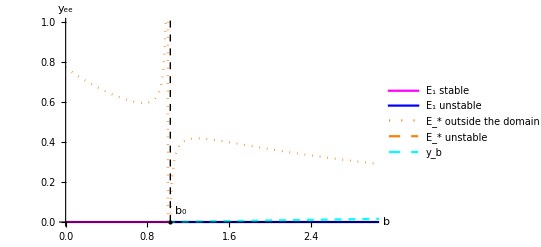

bifEE.pdf

```mathematica
cond=cF1;
Print["roots of Dis[b]=0:", bcE=NSolve[(Dis//.cond)==0,b]]
Print["b0=",bc=b/.Solve[R0==1,b][[1]]//.cond//N]
bL=100; max=2;
bc1=b/.bcE[[5]];
bc2=b/.bcE[[6]];
lin1=Line[{{ bc1,0},{ bc1,max}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,max}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
lin3=Line[{{ bc,0},{ bc,max}}];
li3=Graphics[{Thick,Black,Dashed,lin3}];
p1a=Plot[{ym}//.cond,{b,0,bc1},PlotStyle->{Dashed,Thick,Green},
PlotRange->All,PlotLegends->{"E_- unstable"}];
p1b=Plot[{ym}//.cond,{b,bc1,bL},PlotStyle->{Green},PlotRange->All,
PlotLegends->{"E_- stable"}];
p01=Plot[0,{b,0,bc},PlotStyle->{Magenta},PlotRange->All,PlotLegends->{"E_1 stable"}];
p02=Plot[0,{b,bc,bL},PlotStyle->{Blue},PlotRange->All,PlotLegends->{"E_1 unstable"}];
pp=Plot[{yi}//.cond,{b,0, bL},PlotStyle->{Purple},PlotRange->All,
PlotLegends->{"E_i unstable"}];
pm=Plot[{yp}//.cond,{b,0,bL},PlotStyle->{Red},PlotRange->All,
PlotLegends->{"E_+ unstable"}];
ps1=Plot[{ys}//.cond,{b,0,13.45},PlotStyle->{Orange, Dotted},
PlotRange->{{0,200},{0,max}},
PlotLegends->{"E_* outside the domain"}];
ps2=Plot[{ys}//.cond,{b,13.45,bL},PlotStyle->{Orange,Thick,Dashed},
PlotRange->{{0,200},{0,max}},
PlotLegends->{"E_* unstable"}];

pyb=Plot[{yb}//.cond,{b,0,bL},PlotStyle->{Dashed,Thick,Cyan},
PlotRange->{{0,200},{0,max}},PlotLegends->{"y_b "}];
Print["y*'(b0)=",D[ys,b]/.b->bc//.cond//N//FullSimplify]
Chop[ys/.b->bc//.cond//N](*Check*);
bifE2=Show[{p01,p02,ps1,ps2,pyb,li3},PlotRange->{{0,3},{0,1}},
Epilog->{Text["b_0",Offset[{10,11},{ bc//.cond,0}]],{PointSize[Large],
Style[Point[{ bc//.cond,0}],Black]}},
PlotRange->All,AxesLabel->{"b","y_ee"}]
Export["bifEE.pdf",bifE2]
```

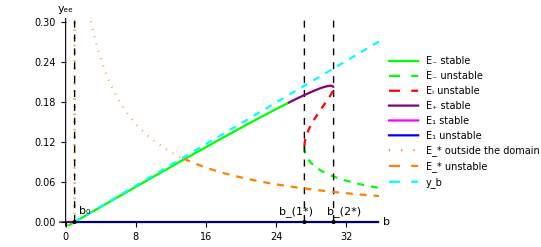

Bnip.pdf

EriB.pdf

```mathematica
p1a=Plot[{ym}//.cond,{b,0,13.45},PlotStyle->{Thick,Green},PlotRange->All];
p1c=Plot[{ym}//.cond,{b,13.45,bc1},PlotStyle->{Thick,Green},
PlotRange->All,PlotLegends->{"E_- stable"}];
p1d=Plot[{ym}//.cond,{b,bc1,bL},PlotStyle->{Dashed,Thick,Green},PlotRange->All,
PlotLegends->{"E_- unstable"}];
pi=Plot[{yi}//.cond,{b,0, bL},PlotStyle->{Dashed,Thick,Red},PlotRange->All,
PlotLegends->{"E_i unstable"}];
pp1=Plot[{yp}//.cond,{b,0,bL},PlotStyle->{Purple},PlotRange->All,
PlotLegends->{"E_+ stable"}];
shon=Show[{p1a,p1c,p1d,li1,li2},PlotRange->{{0,60},{0,0.2}},Epilog->
{{Text["b_(1*)",Offset[{-8,10},{ bc1,0}]],{PointSize[Large],
Style[Point[{ bc1,0}],Purple]},Text["b_(2*)",Offset[{10,10},{ bc2,0}]],
{PointSize[Large],Style[Point[{ bc2,0}],Yellow]}}
},AxesLabel->{"b","y_ee"}];
shoip=Show[{pi,pp1},PlotRange->All,AxesLabel->{"b","y_ee"}];
Bnip=Show[shon,shoip];
EriB=Show[shon,shoip,bifE2,PlotRange->{{0,35},{0,0.3}},Epilog->{
Text["b_0",Offset[{10,11},{ bc//.cond,0}]],{PointSize[Large],
Style[Point[{ bc//.cond,0}],Black]},
Text["b_(1*)",Offset[{-8,10},{ bc1,0}]],{PointSize[Large],
Style[Point[{ bc1,0}],Purple]},
Text["b_(2*)",Offset[{10,10},{ bc2,0}]],{PointSize[Large],
Style[Point[{ bc2,0}],Yellow]}}]
Export["Bnip.pdf",Bnip]
Export["EriB.pdf",EriB]
```